```mathematica
MatrixExp[(KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]+KroneckerProduct[PauliMatrix[2],PauliMatrix[2]])*I*h*J*t/2]//MatrixForm

(*1-qubit matrix*)
m=l
A={{0,m},{Conjugate[m],0}}
B=MatrixExp[A]//FullSimplify
MatrixLog[B]//MatrixForm//FullSimplify

(*What C-NOT gives*)
CNOT=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}})
Xgate=PauliMatrix[1]
Id2=IdentityMatrix[2]
state={1,0,0,0,0,0,0,0}
Amat=KroneckerProduct[Id2,CNOT].KroneckerProduct[CNOT,Id2].KroneckerProduct[Xgate,Id2,Id2]
Amat=KroneckerProduct[Id2,Xgate,Id2].KroneckerProduct[Id2,Id2,Xgate].KroneckerProduct[Xgate,Id2,Id2]
Amat.state
Amat//MatrixForm
Ham=MatrixLog[Amat]/(-I)
Ham//MatrixForm
(*AdjacencyGraph[Amat]*)

AdjacencyGraph[Abs[MatrixLog[Amat]/(-I)]]
```

(1 | 0 | 0 | 0
0 | Cos[h J t] | ⅈ Sin[h J t] | 0
0 | ⅈ Sin[h J t] | Cos[h J t] | 0
0 | 0 | 0 | 1)

l

{{0,l},{Conjugate[l],0}}

{{Cosh[√l √Conjugate[l]],(√l Sinh[√l √Conjugate[l]])/(√Conjugate[l])},{(√Conjugate[l] Sinh[√l √Conjugate[l]])/(√l),Cosh[√l √Conjugate[l]]}}

(1/2 (Log[ⅇ^(-√l √Conjugate[l])]+Log[ⅇ^(√l √Conjugate[l])]) | (√l (-Log[ⅇ^(-√l √Conjugate[l])]+Log[ⅇ^(√l √Conjugate[l])]))/(2 √Conjugate[l])
(√Conjugate[l] (-Log[ⅇ^(-√l √Conjugate[l])]+Log[ⅇ^(√l √Conjugate[l])]))/(2 √l) | 1/2 (Log[ⅇ^(-√l √Conjugate[l])]+Log[ⅇ^(√l √Conjugate[l])]))

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

{{0,1},{1,0}}

{{1,0},{0,1}}

{1,0,0,0,0,0,0,0}

{{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}

{0,0,0,0,0,0,0,1}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{-π/2,0,0,0,0,0,0,π/2},{0,-π/2,0,0,0,0,π/2,0},{0,0,-π/2,0,0,π/2,0,0},{0,0,0,-π/2,π/2,0,0,0},{0,0,0,π/2,-π/2,0,0,0},{0,0,π/2,0,0,-π/2,0,0},{0,π/2,0,0,0,0,-π/2,0},{π/2,0,0,0,0,0,0,-π/2}}

(-π/2 | 0 | 0 | 0 | 0 | 0 | 0 | π/2
0 | -π/2 | 0 | 0 | 0 | 0 | π/2 | 0
0 | 0 | -π/2 | 0 | 0 | π/2 | 0 | 0
0 | 0 | 0 | -π/2 | π/2 | 0 | 0 | 0
0 | 0 | 0 | π/2 | -π/2 | 0 | 0 | 0
0 | 0 | π/2 | 0 | 0 | -π/2 | 0 | 0
0 | π/2 | 0 | 0 | 0 | 0 | -π/2 | 0
π/2 | 0 | 0 | 0 | 0 | 0 | 0 | -π/2)

AdjacencyGraph::inv: The argument {{π/2,0,0,0,0,0,0,π/2},{0,π/2,0,0,0,0,π/2,0},{0,0,π/2,0,0,π/2,0,0},{0,0,0,π/2,π/2,0,0,0},{0,0,0,π/2,π/2,0,0,0},{0,0,π/2,0,0,π/2,0,0},{0,π/2,0,0,0,0,π/2,0},{π/2,0,0,0,0,0,0,π/2}} in AdjacencyGraph[Automatic,{{π/2,0,0,0,0,0,0,π/2},{0,π/2,0,0,0,0,π/2,0},{0,0,π/2,0,0,π/2,0,0},{0,0,0,π/2,π/2,0,0,0},{0,0,0,π/2,π/2,0,0,0},{0,0,π/2,0,0,π/2,0,0},{0,π/2,0,0,0,0,π/2,0},{π/2,0,0,0,0,0,0,π/2}}] is not a valid adjacency matrix.

AdjacencyGraph[Automatic,{{π/2,0,0,0,0,0,0,π/2},{0,π/2,0,0,0,0,π/2,0},{0,0,π/2,0,0,π/2,0,0},{0,0,0,π/2,π/2,0,0,0},{0,0,0,π/2,π/2,0,0,0},{0,0,π/2,0,0,π/2,0,0},{0,π/2,0,0,0,0,π/2,0},{π/2,0,0,0,0,0,0,π/2}}]

```mathematica
P = {{0.924+0.j,-0.383+0.j},{0.383+0.j, 0.924-0.j}}
```

{{0.924,-0.383},{0.383,0.924}}

```mathematica
MatrixForm[P]
```

(0.924 | -0.383
0.383 | 0.924)

```mathematica
MatrixLog[P]
```

```mathematica
{{0.0002324459605017497,-0.3929453938867672},{0.3929453938867673,0.00023244596050165614}}* 5000
```

```mathematica
Simplify[{{1.1622298025087485,-1964.7269694338358},{1964.7269694338365,1.1622298025082807}}]
```

```mathematica
FullSimplify[{{1.1622298025087485,-1964.7269694338358},{1964.7269694338365,1.1622298025082807}}]
```

{{1.16223,-1964.73},{1964.73,1.16223}}

```mathematica
AdjacencyGraph[{{7 ,1965},{1965,7}}]
```

-Graphics-

```mathematica
{{0.+0.0002324459605017497 ⅈ,0.-0.3929453938867672 ⅈ},{0.+0.3929453938867673 ⅈ,0.+0.00023244596050165614 ⅈ}}*5000
```

{{0.+1.16223 ⅈ,0.-1964.73 ⅈ},{0.+1964.73 ⅈ,0.+1.16223 ⅈ}}

```mathematica
MatrixForm[{{0.0002324459605017497,-0.3929453938867672},{0.3929453938867673,0.00023244596050165614}}]
```

(0.000232446 | -0.392945
0.392945 | 0.000232446)

```mathematica
AdjacencyGraph[{{0.000232445960501749ⅈ,-0.3929453938867672 ⅈ},{0.3929453938867673 ⅈ,0.00023244596050165614 ⅈ}}]
```

AdjacencyGraph::inv: The argument {{0.+0.000232446 ⅈ,0.-0.392945 ⅈ},{0.+0.392945 ⅈ,0.+0.000232446 ⅈ}} in AdjacencyGraph[Automatic,{{0.+0.000232446 ⅈ,0.-0.392945 ⅈ},{0.+0.392945 ⅈ,0.+0.000232446 ⅈ}}] is not a valid adjacency matrix.

AdjacencyGraph[Automatic,{{0.+0.000232446 ⅈ,0.-0.392945 ⅈ},{0.+0.392945 ⅈ,0.+0.000232446 ⅈ}}]

```mathematica
AdjacencyGraph[{{Abs[5ⅈ], 1}, {3, 3}}]
```

-Graphics-

```mathematica
Abs[3ⅈ]
```

3

```mathematica
a[t_,p_,l_] := {{1/2 ⅈ (-4 Log[2]+Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]-ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]+(√2 ⅇ^(ⅈ l) (-1+ⅇ^(ⅈ (l+p))) Cos[t/2] (Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]-ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]-Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]+ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]))/(√(ⅇ^(2 ⅈ l) (1+Cos[t])+ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-2 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t]))))+Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]+ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]),-((2 ⅈ (Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]-ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]-Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]+ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]) Sin[t/2])/(√(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))))},{-((ⅈ √2 ⅇ^(ⅈ (l+p)) (Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]-ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]-Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]+ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]) Sin[t/2])/(√(ⅇ^(2 ⅈ l) (1+Cos[t])+ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-2 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t]))))),-((ⅈ ⅇ^(ⅈ l) (-1+ⅇ^(ⅈ (l+p))) Cos[t/2] (Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]-ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]-Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]+ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]))/(√2 √(ⅇ^(2 ⅈ l) (1+Cos[t])+ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-2 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))))+1/2 ⅈ (-2 Log[4]+Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]-ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))]+Log[2 (1+ⅇ^(ⅈ (l+p))) Cos[t/2]+ⅇ^(-ⅈ l) √(2 ⅇ^(2 ⅈ l) (1+Cos[t])+2 ⅇ^(2 ⅈ (2 l+p)) (1+Cos[t])-4 ⅇ^(ⅈ (l+p)) (2 (-1+Cos[t])+ⅇ^(2 ⅈ l) (1+Cos[t])))])}}
```

```mathematica
A = Block[{$MaxExtraPrecision= 10000000000},N[a[3*(Pi/3),0,pi]]]
```

{{(0.+0.5 ⅈ) (-2.77259+Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]+Log[4./(√(2.71828^((0.+1. ⅈ) pi)))]),-((0.+0.5 ⅈ) (Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]-1. Log[4./(√(2.71828^((0.+1. ⅈ) pi)))]))/(√(2.71828^((0.+1. ⅈ) pi)))},{(0.-0.5 ⅈ) √(2.71828^((0.+1. ⅈ) pi)) (Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]-1. Log[4./(√(2.71828^((0.+1. ⅈ) pi)))]),(0.+0.5 ⅈ) (-2.77259+Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]+Log[4./(√(2.71828^((0.+1. ⅈ) pi)))])}}

```mathematica
{{(1,(0.7071067811865476+0.7071067811865475 ⅈ) ∞},{(-0.7071067811865475+0.7071067811865475 ⅈ) ∞,-∞+(-ⅈ) ∞}}
```

```mathematica
{{-1.1780972450961724+0. ⅈ,-0.6011177298843463-1.4512265760697154 ⅈ},{-0.6011177298843463+1.4512265760697154 ⅈ,-1.1780972450961724+0. ⅈ}}
```

{{-1.1781+0. ⅈ,-0.601118-1.45123 ⅈ},{-0.601118+1.45123 ⅈ,-1.1781+0. ⅈ}}

```mathematica
{{-2.7755575615628914*^-16-1.1102230246251565*^-16 ⅈ,0.},{0.,-2.356194490192345+1.6653345369377348*^-16 ⅈ}}
```

{{-2.77556×10^-16-1.11022×10^-16 ⅈ,0.},{0.,-2.35619+1.66533×10^-16 ⅈ}}

```mathematica
func[x_]:=If[Abs[x]>0.01,1,0];
B=Map[func,A,{2}]
```

{{If[0.5 Abs[-2.77259+Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]+Log[4./(√(2.71828^((0.+1. ⅈ) pi)))]]>0.01,1,0],If[(0.5 Abs[Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]-1. Log[4./(√(2.71828^((0.+1. ⅈ) pi)))]])/(√(2.71828^Re[(0.+1. ⅈ) pi]))>0.01,1,0]},{If[0.5 √(2.71828^Re[(0.+1. ⅈ) pi]) Abs[Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]-1. Log[4./(√(2.71828^((0.+1. ⅈ) pi)))]]>0.01,1,0],If[0.5 Abs[-2.77259+Log[-4./(√(2.71828^((0.+1. ⅈ) pi)))]+Log[4./(√(2.71828^((0.+1. ⅈ) pi)))]]>0.01,1,0]}}

{{1,1},{1,1}}

{1,0}

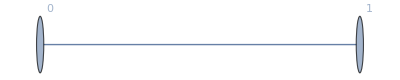

```mathematica
{{1,1},{1,1}}
vl = {"1", "0"}
AdjacencyGraph[{{0, 1},{ 1,0}},VertexLabels->Table[i-> vl[[i]],{i,Length[vl]}]]
```

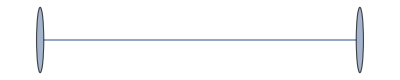
```mathematica
-Graphics-    (*(Pi,0,Pi)*) (*Pi/32,0,0*) (*Pi/64,0,0*)
AdjacencyGraph[{{1,1},{1,1}}]
```

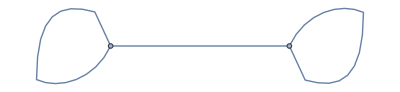
```mathematica
-Graphics-(*Pi,Pi/2,Pi*) (*Pi,3*(Pi/4),Pi*)(*Pi,0,0*)(*3*(Pi/4),Pi/2,0*)
(*Pi/8,0,Pi/8*)
```

```mathematica
AdjacencyGraph[{{0,0},{0,1}}]
```

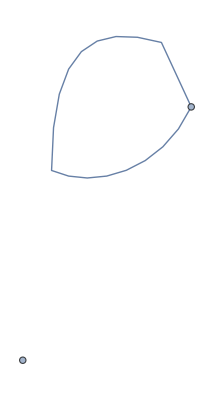
```mathematica
-Graphics-(**z=(0,0,Pi)**) (*0,3*(Pi/4),Pi*) (*0,Pi/4,0*) (*0,Pi,0*)
```

```mathematica
AdjacencyGraph[{{1,1},{1,1}}]
```

```mathematica
-Graphics-(**(Pi, Pi,Pi),y**)(*Pi,3*(Pi/4),0*)(*Pi/2,0,Pi/2*)
(*3*(Pi/4),0,Pi/2*)
```

```mathematica
AdjacencyGraph[{{0,1},{0,1}}]
```

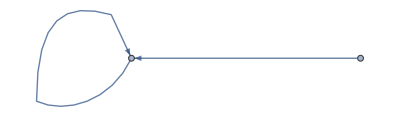
```mathematica
-Graphics-(* *(0, 0,3*(Pi/4))**)
```

```mathematica
H = [[0.+0.j,1.+0.j,0.+0.j,0.+0.j],[0.+0.j,0.+0.j,1.+0.j,0.+0.j],[0.+0.j,0.+0.j,0.+0.j,1.+0.j],[1.+0.j,0.+0.j,0.+0.j,0.+0.j]]
```

```mathematica
H = {{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}}
```

{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}}

```mathematica
MatrixForm[H]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

```mathematica
MatrixLog[{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}}]
```

```mathematica
A = {{(ⅈ π)/4,(1/4-ⅈ/4) π,(ⅈ π)/4,(-1/4-ⅈ/4) π},{(-1/4-ⅈ/4) π,(ⅈ π)/4,(1/4-ⅈ/4) π,(ⅈ π)/4},{(ⅈ π)/4,(-1/4-ⅈ/4) π,(ⅈ π)/4,(1/4-ⅈ/4) π},{(1/4-ⅈ/4) π,(ⅈ π)/4,(-1/4-ⅈ/4) π,(ⅈ π)/4}}
```

```mathematica
I*{{(ⅈ π)/4,(1/4-ⅈ/4) π,(ⅈ π)/4,(-1/4-ⅈ/4) π},{(-1/4-ⅈ/4) π,(ⅈ π)/4,(1/4-ⅈ/4) π,(ⅈ π)/4},{(ⅈ π)/4,(-1/4-ⅈ/4) π,(ⅈ π)/4,(1/4-ⅈ/4) π},{(1/4-ⅈ/4) π,(ⅈ π)/4,(-1/4-ⅈ/4) π,(ⅈ π)/4}}
```

{{-π/4,(1/4+ⅈ/4) π,-π/4,(1/4-ⅈ/4) π},{(1/4-ⅈ/4) π,-π/4,(1/4+ⅈ/4) π,-π/4},{-π/4,(1/4-ⅈ/4) π,-π/4,(1/4+ⅈ/4) π},{(1/4+ⅈ/4) π,-π/4,(1/4-ⅈ/4) π,-π/4}}

```mathematica
MatrixForm[{{-π/4,(1/4+ⅈ/4) π,-π/4,(1/4-ⅈ/4) π},{(1/4-ⅈ/4) π,-π/4,(1/4+ⅈ/4) π,-π/4},{-π/4,(1/4-ⅈ/4) π,-π/4,(1/4+ⅈ/4) π},{(1/4+ⅈ/4) π,-π/4,(1/4-ⅈ/4) π,-π/4}}]
```

(-π/4 | (1/4+ⅈ/4) π | -π/4 | (1/4-ⅈ/4) π
(1/4-ⅈ/4) π | -π/4 | (1/4+ⅈ/4) π | -π/4
-π/4 | (1/4-ⅈ/4) π | -π/4 | (1/4+ⅈ/4) π
(1/4+ⅈ/4) π | -π/4 | (1/4-ⅈ/4) π | -π/4)

```mathematica
MatrixForm[A]
```

((ⅈ π)/4 | (1/4-ⅈ/4) π | (ⅈ π)/4 | (-1/4-ⅈ/4) π
(-1/4-ⅈ/4) π | (ⅈ π)/4 | (1/4-ⅈ/4) π | (ⅈ π)/4
(ⅈ π)/4 | (-1/4-ⅈ/4) π | (ⅈ π)/4 | (1/4-ⅈ/4) π
(1/4-ⅈ/4) π | (ⅈ π)/4 | (-1/4-ⅈ/4) π | (ⅈ π)/4)

```mathematica
func[x_]:=If[Abs[x]>0.01,1,0];
B=Map[func,A,{2}]
```

```mathematica
{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
MatrixForm[{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}]
```

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)

```mathematica
B
```

{{(ⅈ π)/4,(1/4-ⅈ/4) π,(ⅈ π)/4,(-1/4-ⅈ/4) π},{(-1/4-ⅈ/4) π,(ⅈ π)/4,(1/4-ⅈ/4) π,(ⅈ π)/4},{(ⅈ π)/4,(-1/4-ⅈ/4) π,(ⅈ π)/4,(1/4-ⅈ/4) π},{(1/4-ⅈ/4) π,(ⅈ π)/4,(-1/4-ⅈ/4) π,(ⅈ π)/4}}

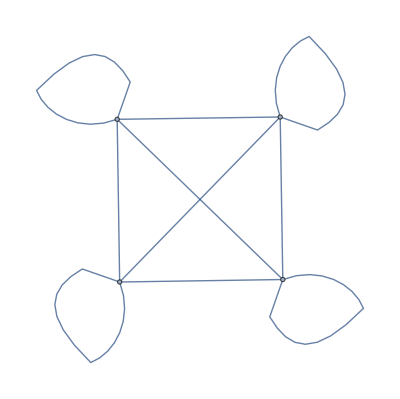

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
AdjacencyGraph[{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}]
```

```mathematica
J = {{0, 0, 1, 0}, {0, 0, 0, 1}, {0, 1, 0, 0}, {1, 0, 0, 0}}
```

{{0,0,1,0},{0,0,0,1},{0,1,0,0},{1,0,0,0}}

```mathematica
MatrixForm[J]
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
MatrixLog[{{0,0,1,0},{0,0,0,1},{0,1,0,0},{1,0,0,0}}]
```

```mathematica
A = {{(ⅈ π)/4,(ⅈ π)/4,(1/4-ⅈ/4) π,(-1/4-ⅈ/4) π},{(ⅈ π)/4,(ⅈ π)/4,(-1/4-ⅈ/4) π,(1/4-ⅈ/4) π},{(-1/4-ⅈ/4) π,(1/4-ⅈ/4) π,(ⅈ π)/4,(ⅈ π)/4},{(1/4-ⅈ/4) π,(-1/4-ⅈ/4) π,(ⅈ π)/4,(ⅈ π)/4}}
```

{{(ⅈ π)/4,(ⅈ π)/4,(1/4-ⅈ/4) π,(-1/4-ⅈ/4) π},{(ⅈ π)/4,(ⅈ π)/4,(-1/4-ⅈ/4) π,(1/4-ⅈ/4) π},{(-1/4-ⅈ/4) π,(1/4-ⅈ/4) π,(ⅈ π)/4,(ⅈ π)/4},{(1/4-ⅈ/4) π,(-1/4-ⅈ/4) π,(ⅈ π)/4,(ⅈ π)/4}}

```mathematica
{{0,0,0,0,0,0, 0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}
```

{{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[{{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixLog[{{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}]
```

```mathematica
A = {{(ⅈ π)/2,0,0,0,0,0,0,-(ⅈ π)/2},{0,(ⅈ π)/2,0,0,0,0,-(ⅈ π)/2,0},{0,0,(ⅈ π)/2,0,0,-(ⅈ π)/2,0,0},{0,0,0,(ⅈ π)/2,-(ⅈ π)/2,0,0,0},{0,0,0,-(ⅈ π)/2,(ⅈ π)/2,0,0,0},{0,0,-(ⅈ π)/2,0,0,(ⅈ π)/2,0,0},{0,-(ⅈ π)/2,0,0,0,0,(ⅈ π)/2,0},{-(ⅈ π)/2,0,0,0,0,0,0,(ⅈ π)/2}}
```

{{(ⅈ π)/2,0,0,0,0,0,0,-(ⅈ π)/2},{0,(ⅈ π)/2,0,0,0,0,-(ⅈ π)/2,0},{0,0,(ⅈ π)/2,0,0,-(ⅈ π)/2,0,0},{0,0,0,(ⅈ π)/2,-(ⅈ π)/2,0,0,0},{0,0,0,-(ⅈ π)/2,(ⅈ π)/2,0,0,0},{0,0,-(ⅈ π)/2,0,0,(ⅈ π)/2,0,0},{0,-(ⅈ π)/2,0,0,0,0,(ⅈ π)/2,0},{-(ⅈ π)/2,0,0,0,0,0,0,(ⅈ π)/2}}

```mathematica
func[x_]:=If[Abs[x]>0.01,1,0];
B=Map[func,A,{2}]
```

{{1,0,0,0,0,0,0,1},{0,1,0,0,0,0,1,0},{0,0,1,0,0,1,0,0},{0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0},{0,0,1,0,0,1,0,0},{0,1,0,0,0,0,1,0},{1,0,0,0,0,0,0,1}}

```mathematica
MatrixForm[B]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

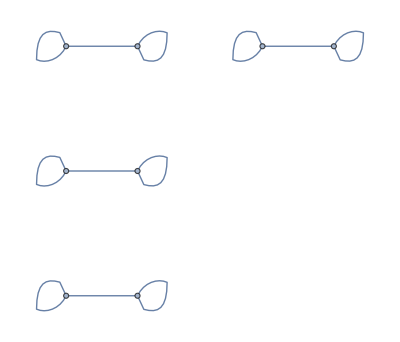

```mathematica
AdjacencyGraph[{{1,0,0,0,0,0,0,1},{0,1,0,0,0,0,1,0},{0,0,1,0,0,1,0,0},{0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0},{0,0,1,0,0,1,0,0},{0,1,0,0,0,0,1,0},{1,0,0,0,0,0,0,1}}]
```

```mathematica
K = {{0,0,1,0,0,0, 0,0},{0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0}}
MatrixLog[{{0,0,1,0,0,0, 0,0},{0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0}}]
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0}}

MatrixLog::fnanc: The function Log is not analytic at 0.

```mathematica
M[k_, m_] := 2*Pi*{{k+m,m, m , m}, {m,k+m, m , m}, {m,m, k+m , m}, {m,m, m , k+m}}
```

```mathematica
A = 4*{{-π/4,(1/4+ⅈ/4) π,-π/4,(1/4-ⅈ/4) π},{(1/4-ⅈ/4) π,-π/4,(1/4+ⅈ/4) π,-π/4},{-π/4,(1/4-ⅈ/4) π,-π/4,(1/4+ⅈ/4) π},{(1/4+ⅈ/4) π,-π/4,(1/4-ⅈ/4) π,-π/4}} +  M[0,1/2]
```

{{0,(2+ⅈ) π,0,(2-ⅈ) π},{(2-ⅈ) π,0,(2+ⅈ) π,0},{0,(2-ⅈ) π,0,(2+ⅈ) π},{(2+ⅈ) π,0,(2-ⅈ) π,0}}

```mathematica
func[x_]:=If[Abs[x]>0.01,1,0];
B=Map[func,A,{2}]
```

```mathematica
{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}
```

{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}

```mathematica
MatrixForm[B]
```

(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

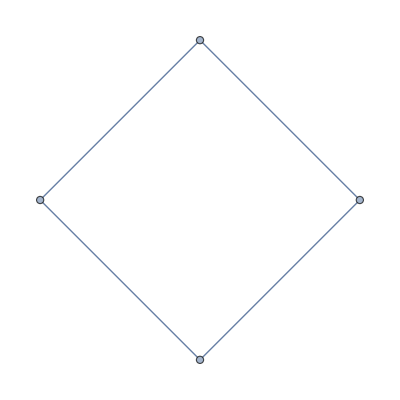

```mathematica
AdjacencyGraph[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}]
```

```mathematica
StringReplace[ToString@lst,{"["->"{","]"->"}"}]
```

lst

```mathematica
var={{1,{1,0}},{2,{0,0,0}},{3,{2,3}},{4,{4,5,6}},{5,{7,8,9}}}
```

{{1,{1,0}},{2,{0,0,0}},{3,{2,3}},{4,{4,5,6}},{5,{7,8,9}}}

```mathematica
U = {{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
```

{{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[U]
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixLog[{{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]
```

```mathematica
I*{{(ⅈ π)/4,0,0,0,0,0,(1/4-ⅈ/4) π,0,0,(ⅈ π)/4,0,0,0,0,0,(-1/4-ⅈ/4) π},{0,(ⅈ π)/4,0,0,0,0,0,(1/4-ⅈ/4) π,(ⅈ π)/4,0,0,0,0,0,(-1/4-ⅈ/4) π,0},{0,0,(ⅈ π)/4,0,(-1/4-ⅈ/4) π,0,0,0,0,0,0,(ⅈ π)/4,0,(1/4-ⅈ/4) π,0,0},{0,0,0,(ⅈ π)/4,0,(-1/4-ⅈ/4) π,0,0,0,0,(ⅈ π)/4,0,(1/4-ⅈ/4) π,0,0,0},{0,0,(1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0,0,0,0,0,(-1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0},{0,0,0,(1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0,0,0,(-1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0,0},{(-1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4,0,0,(1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4},{0,(-1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4,(1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4,0},{0,(ⅈ π)/4,0,0,0,0,0,(-1/4-ⅈ/4) π,(ⅈ π)/4,0,0,0,0,0,(1/4-ⅈ/4) π,0},{(ⅈ π)/4,0,0,0,0,0,(-1/4-ⅈ/4) π,0,0,(ⅈ π)/4,0,0,0,0,0,(1/4-ⅈ/4) π},{0,0,0,(ⅈ π)/4,0,(1/4-ⅈ/4) π,0,0,0,0,(ⅈ π)/4,0,(-1/4-ⅈ/4) π,0,0,0},{0,0,(ⅈ π)/4,0,(1/4-ⅈ/4) π,0,0,0,0,0,0,(ⅈ π)/4,0,(-1/4-ⅈ/4) π,0,0},{0,0,0,(-1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0,0,0,(1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0,0},{0,0,(-1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0,0,0,0,0,(1/4-ⅈ/4) π,0,(ⅈ π)/4,0,0},{0,(1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4,(-1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4,0},{(1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4,0,0,(-1/4-ⅈ/4) π,0,0,0,0,0,(ⅈ π)/4}}
```

```mathematica
A = {{-π/4,0,0,0,0,0,(1/4+ⅈ/4) π,0,0,-π/4,0,0,0,0,0,(1/4-ⅈ/4) π},{0,-π/4,0,0,0,0,0,(1/4+ⅈ/4) π,-π/4,0,0,0,0,0,(1/4-ⅈ/4) π,0},{0,0,-π/4,0,(1/4-ⅈ/4) π,0,0,0,0,0,0,-π/4,0,(1/4+ⅈ/4) π,0,0},{0,0,0,-π/4,0,(1/4-ⅈ/4) π,0,0,0,0,-π/4,0,(1/4+ⅈ/4) π,0,0,0},{0,0,(1/4+ⅈ/4) π,0,-π/4,0,0,0,0,0,0,(1/4-ⅈ/4) π,0,-π/4,0,0},{0,0,0,(1/4+ⅈ/4) π,0,-π/4,0,0,0,0,(1/4-ⅈ/4) π,0,-π/4,0,0,0},{(1/4-ⅈ/4) π,0,0,0,0,0,-π/4,0,0,(1/4+ⅈ/4) π,0,0,0,0,0,-π/4},{0,(1/4-ⅈ/4) π,0,0,0,0,0,-π/4,(1/4+ⅈ/4) π,0,0,0,0,0,-π/4,0},{0,-π/4,0,0,0,0,0,(1/4-ⅈ/4) π,-π/4,0,0,0,0,0,(1/4+ⅈ/4) π,0},{-π/4,0,0,0,0,0,(1/4-ⅈ/4) π,0,0,-π/4,0,0,0,0,0,(1/4+ⅈ/4) π},{0,0,0,-π/4,0,(1/4+ⅈ/4) π,0,0,0,0,-π/4,0,(1/4-ⅈ/4) π,0,0,0},{0,0,-π/4,0,(1/4+ⅈ/4) π,0,0,0,0,0,0,-π/4,0,(1/4-ⅈ/4) π,0,0},{0,0,0,(1/4-ⅈ/4) π,0,-π/4,0,0,0,0,(1/4+ⅈ/4) π,0,-π/4,0,0,0},{0,0,(1/4-ⅈ/4) π,0,-π/4,0,0,0,0,0,0,(1/4+ⅈ/4) π,0,-π/4,0,0},{0,(1/4+ⅈ/4) π,0,0,0,0,0,-π/4,(1/4-ⅈ/4) π,0,0,0,0,0,-π/4,0},{(1/4+ⅈ/4) π,0,0,0,0,0,-π/4,0,0,(1/4-ⅈ/4) π,0,0,0,0,0,-π/4}}
```

{{-π/4,0,0,0,0,0,(1/4+ⅈ/4) π,0,0,-π/4,0,0,0,0,0,(1/4-ⅈ/4) π},{0,-π/4,0,0,0,0,0,(1/4+ⅈ/4) π,-π/4,0,0,0,0,0,(1/4-ⅈ/4) π,0},{0,0,-π/4,0,(1/4-ⅈ/4) π,0,0,0,0,0,0,-π/4,0,(1/4+ⅈ/4) π,0,0},{0,0,0,-π/4,0,(1/4-ⅈ/4) π,0,0,0,0,-π/4,0,(1/4+ⅈ/4) π,0,0,0},{0,0,(1/4+ⅈ/4) π,0,-π/4,0,0,0,0,0,0,(1/4-ⅈ/4) π,0,-π/4,0,0},{0,0,0,(1/4+ⅈ/4) π,0,-π/4,0,0,0,0,(1/4-ⅈ/4) π,0,-π/4,0,0,0},{(1/4-ⅈ/4) π,0,0,0,0,0,-π/4,0,0,(1/4+ⅈ/4) π,0,0,0,0,0,-π/4},{0,(1/4-ⅈ/4) π,0,0,0,0,0,-π/4,(1/4+ⅈ/4) π,0,0,0,0,0,-π/4,0},{0,-π/4,0,0,0,0,0,(1/4-ⅈ/4) π,-π/4,0,0,0,0,0,(1/4+ⅈ/4) π,0},{-π/4,0,0,0,0,0,(1/4-ⅈ/4) π,0,0,-π/4,0,0,0,0,0,(1/4+ⅈ/4) π},{0,0,0,-π/4,0,(1/4+ⅈ/4) π,0,0,0,0,-π/4,0,(1/4-ⅈ/4) π,0,0,0},{0,0,-π/4,0,(1/4+ⅈ/4) π,0,0,0,0,0,0,-π/4,0,(1/4-ⅈ/4) π,0,0},{0,0,0,(1/4-ⅈ/4) π,0,-π/4,0,0,0,0,(1/4+ⅈ/4) π,0,-π/4,0,0,0},{0,0,(1/4-ⅈ/4) π,0,-π/4,0,0,0,0,0,0,(1/4+ⅈ/4) π,0,-π/4,0,0},{0,(1/4+ⅈ/4) π,0,0,0,0,0,-π/4,(1/4-ⅈ/4) π,0,0,0,0,0,-π/4,0},{(1/4+ⅈ/4) π,0,0,0,0,0,-π/4,0,0,(1/4-ⅈ/4) π,0,0,0,0,0,-π/4}}

```mathematica
func[x_]:=If[Abs[x]>0.01,1,0];
B=Map[func,A,{2}]
```

{{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1}}

```mathematica
MatrixForm[B]
```

(1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1)

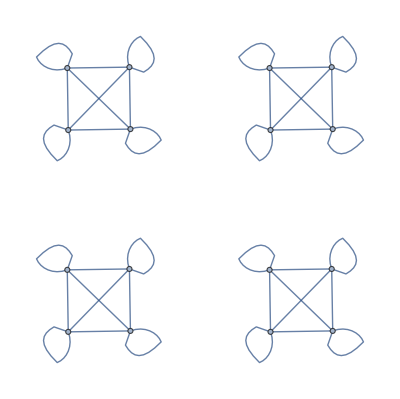

```mathematica
AdjacencyGraph[{{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1}}]
```

```mathematica
MatrixLog[{{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]
```

$Aborted